```mathematica
Clear["Global`*"]
```

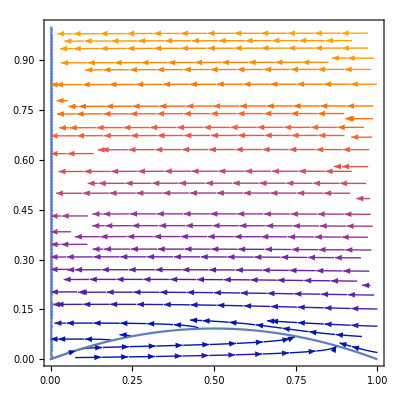

```mathematica
Block[{ϵ=0.01,f=2.7,q=0.0002},Show[StreamPlot[{(1/ϵ)(x-x^2-f z (x-q)/(x+q)),x-z},{x,0,1},{z,0,1}],ContourPlot[{(x-x^2-(f (-q+x) z)/(q+x))/ϵ==0,h[x,z]==0},{x,0,1},{z,0,1}]]]
```

## Oscillation

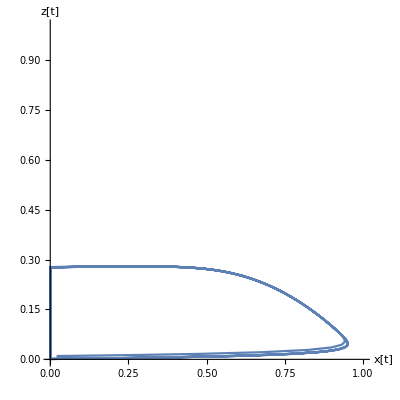
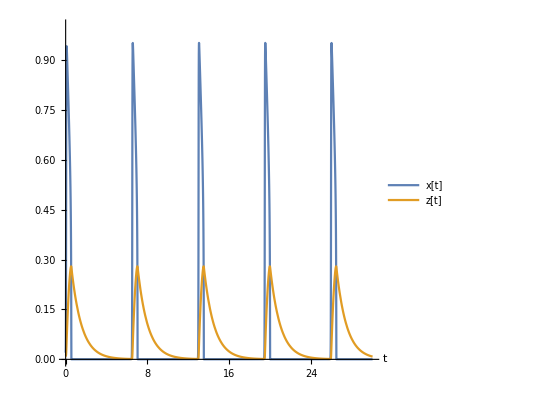

```mathematica
Clear["Global`*"]
Block[{ϵ=0.01,f=1,q=0.0002},time=30;s=NDSolve[{x'[t]==(1/ϵ)(x[t]-x[t]^2-f z[t] (x[t]-q)/(x[t]+q)),z'[t]==x[t]-z[t],x[0]==0.02,z[0]==0.01},{x,z},{t,time}];{ParametricPlot[Evaluate[{x[t],z[t]}/.s],{t,0,time},PlotRange->{{0,1},{0,1}},AxesLabel->{"x[t]","z[t]"}],ParametricPlot[Evaluate[{{t,x[t]/.s},{t,z[t]/.s}}],{t,0,time},PlotRange->{{0,time},{0,1}},AspectRatio->1,AxesLabel->{"t"},PlotLegends->{"x[t]","z[t]"}]}]
```

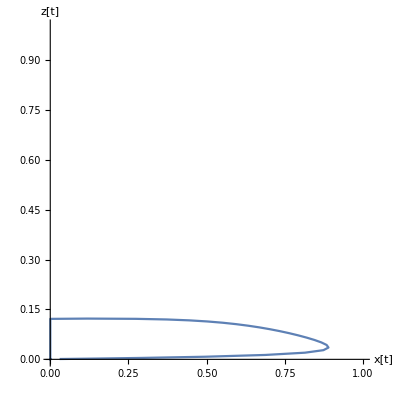
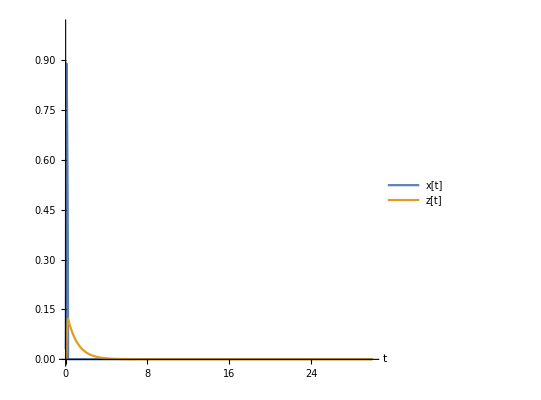

```mathematica
Block[{ϵ=0.01,f=2.7,q=0.0002},time=30;s=NDSolve[{x'[t]==(1/ϵ)(x[t]-x[t]^2-f z[t] (x[t]-q)/(x[t]+q)),z'[t]==x[t]-z[t],x[0]==0.03,z[0]==0.001},{x,z},{t,time}];{ParametricPlot[Evaluate[{x[t],z[t]}/.s],{t,0,time},PlotRange->{{0,1},{0,1}},AxesLabel->{"x[t]","z[t]"}],ParametricPlot[Evaluate[{{t,x[t]/.s},{t,z[t]/.s}}],{t,0,time},PlotRange->{{0,time},{0,1}},AspectRatio->1,AxesLabel->{"t"},PlotLegends->{"x[t]","z[t]"}]}]
```

The following code takes minutes to run. Consider shorten the time `tt`.

```mathematica
Block[{ϵ=0.01,f=2.7,q=0.0002,dt=0.00001,tt=3000000},
evolve=Compile[{{x,_Real},{z,_Real}},{x+dt*(1/ϵ)(x-x^2-f z (x-q)/(x+q))+dt*Exp[RandomVariate[NormalDistribution[0,1]]],z+dt*(x-z)}];ls=NestList[evolve@@#&,{0.03,0.001},tt];
{ListPlot[ls,PlotRange->{{0,1},{0,1}}],
ListPlot[{
Thread[{Range[0,tt]*dt,ls[[All,1]]}],
Thread[{Range[0,tt]*dt,ls[[All,2]]}]
},PlotRange->{{0,tt*dt},{0,1}}]}
](* Takes minutes *)
```